# Superluminality and dispersion relations for non-local field theory

## Setup

```mathematica
$Assumptions=And[ω>0];
```

```mathematica
(*path=NotebookDirectory[]<>"../notes-common/figs/";*)
path=NotebookDirectory[];
```

## Formulas

```mathematica
ProductLog[-π/2]
Limit[ProductLog[α ⅇ^(2 r^2 ϵ) r^2 ϵ]/r^2,r->0]
(*Limit[ProductLog[-4 ⅇ^(2 r^2) r^2],r->∞]*)
Limit[ProductLog[-α ⅇ^(-2 r^2) r^2]/r^2,r->∞]

ProductLog[-4 ⅇ^(2 r^2) r^2]/(2 r^2)/.{r->1000}//N
```

(ⅈ π)/2

α ϵ

0

1.+1.5708×10^-6 ⅈ

## Dispersion relations: constant background

### Parameters

- ϵ=+1 for positive mass-squared field
- ϵ=-1 for negative mass-squared field (tachyon)
- η : turns on and off the mass in the exponential
- ξ : non-locality parameter

```mathematica
posMassRep={ϵ->1};
negMassRep={ϵ->-1};

noMassExpRep={η->0};
massExpRep={η->1};

localRep={ξ->0};
```

```mathematica
localDev[f_,n_:2]:=Series[f,{ξ,0,n}]
```

### Equations of motion

Potential

```mathematica
V[ϕ_]:=ϵ/2 ϕ^2-1/3 ⅇ^(-3η ϵ ξ^2)ϕ^3
```

Equation of motion

```mathematica
ℰ[ϕ_]:=k^2 ϕ+ϵ ϕ-ⅇ^(-2 ξ^2 k^2-3η ϵ ξ^2)ϕ^2
ℰ[ϕ]
```

k^2 ϕ+ϵ ϕ-ⅇ^(-2 k^2 ξ^2-3 ϵ η ξ^2) ϕ^2

Constant background

```mathematica
ϕ0=ϕ/.Solve[ℰ[ϕ]==0/.k->0,ϕ][[2]]
```

ⅇ^(3 ϵ η ξ^2) ϵ

Linearized equation of motion

```mathematica
ℰl[ϕ_]:=Series[ℰ[ϕ0+ϕ],{ϕ,0,1}]//Normal
ℰl[ϕ]
```

ⅇ^(-2 k^2 ξ^2+3 ϵ η ξ^2) ϵ (ⅇ^(2 k^2 ξ^2) k^2-ϵ+ⅇ^(2 k^2 ξ^2) ϵ)+(k^2+ϵ-2 ⅇ^(-2 k^2 ξ^2) ϵ) ϕ

Dispersion relation

```mathematica
dispEq=Coefficient[ℰl[ϕ],ϕ]
```

k^2+ϵ-2 ⅇ^(-2 k^2 ξ^2) ϵ

## Dispersion relations

### Solution for the refractive index

Write the dispersion relation in terms of the refractive index.

```mathematica
nEq[ω_]:=dispEq/.k->√(ω^2(-1+n[ω]^2))//Simplify
-nEq[ω]/ω^2+n[ω]^2//Expand
```

1-ϵ/ω^2+(2 ⅇ^(-2 ξ^2 ω^2 (-1+n[ω]^2)) ϵ)/ω^2

Solution to refractive index.

```mathematica
nSolRep=Solve[nEq[ω]==0,n[ω]][[2]]//Simplify
nSol[ω_]=n[ω]/.nSolRep//Simplify;
vpSol[ω_]:=1/nSol[ω]
vgSol[ω_]:=1/(nSol[ω]+ω D[nSol[ω], ω])
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{n[ω]→(√(ξ^2 (-ϵ+ω^2)+1/2 ProductLog[4 ⅇ^(2 ϵ ξ^2) ϵ ξ^2]))/(ξ ω)}

```mathematica
vpSol[ω]^2==1/vgSol[ω]^2//Simplify//FullSimplify
```

True

The Lambert function is multi-valued. It seems that when the argument is lower than -1/ⅇ, it is better to use the branch n = -1.

```mathematica
nSolBr[ω_]:=nSol[ω]/.ProductLog[z_]->ProductLog[-1,z]
```

Refractive index and velocities for the local theory

```mathematica
nl[ω_]:=√(localDev[ nSol[ω]^2,0]//Normal);
vpl[ω_]:=√(localDev[ vpSol[ω]^2,0]//Normal);
vgl[ω_]:=√(localDev[ vgSol[ω]^2,0]//Normal);
```

```mathematica
vpl[ω]//PowerExpand
vgl[ω]==1/vpl[ω]//PowerExpand
nl[ω]//PowerExpand
```

ω/(√(ϵ+ω^2))

True

(√(ϵ+ω^2))/ω

The non-local interaction behaves like an effective mass, which we extract here. The first term is just the mass from the quadratic action, the second is a combination of background + interaction + non-locality.

```mathematica
meff2=ω^2(1-nSol[ω]^2)//Simplify
meff2Br=ω^2(1-nSolBr[ω]^2)//Simplify
```

ϵ-ProductLog[4 ⅇ^(2 ϵ ξ^2) ϵ ξ^2]/(2 ξ^2)

ϵ-ProductLog[-1,4 ⅇ^(2 ϵ ξ^2) ϵ ξ^2]/(2 ξ^2)

```mathematica
localDev[meff2]
```

-ϵ+4 ϵ^2 ξ^2+O[ξ]^3

We extract the argument of Lambert’s function such that we can analyze when the function becomes complex.
This never happens in the positive mass-squared case because the argument is always positive. In the tachyonic case, there are two possible values and we need to select the lowest one for the critical value.

```mathematica
Warg=(2 ξ^2(ϵ-meff2))[[1]]
ξcAllRep=Solve[Warg==-1/ⅇ,ξ]
ξ^2/.ξcAllRep//N
```

4 ⅇ^(2 ϵ ξ^2) ϵ ξ^2

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{ξ→-(√(1/2 ProductLog[-1/(2 ⅇ)]))/(√ϵ)},{ξ→(√(1/2 ProductLog[-1/(2 ⅇ)]))/(√ϵ)},{ξ→-(√(1/2 ProductLog[-1,-1/(2 ⅇ)]))/(√ϵ)},{ξ→(√(1/2 ProductLog[-1,-1/(2 ⅇ)]))/(√ϵ)}}

{-0.11598/ϵ,-0.11598/ϵ,-1.33917/ϵ,-1.33917/ϵ}

```mathematica
ξcRep={ξ->-(ξ/.ξcAllRep[[1]])/.negMassRep};
ξc=ξ/.ξcRep
ξc//N
ξc^2//N

Warg==-1/ⅇ/.ξcRep/.negMassRep//N;
```

-ⅈ √(1/2 ProductLog[-1/(2 ⅇ)])

0.340559+0. ⅈ

0.11598

```mathematica
ξc2Rep={ξ->-(ξ/.ξcAllRep[[3]])/.negMassRep};
ξc2=ξ/.ξc2Rep
ξc2//N
ξc2^2//N
```

-ⅈ √(1/2 ProductLog[-1,-1/(2 ⅇ)])

1.15723+0. ⅈ

1.33917

```mathematica
(*Warg==-π/2/.negMassRep
Solve[Warg==-π/2/.negMassRep]*)
(*meff2/.Warg->-π/2/.negMassRep
√(ξ^2+0.186319417545)/.ξcRep/.negMassRep//N
Warg/.ξ->%/.negMassRep*)
```

### Positive mass-squared

Local limit

```mathematica
m02=localDev[meff2/.posMassRep,0]//Normal
```

-1

```mathematica
localDev[meff2/.posMassRep]
localDev[√(localDev[ nSol[ω]^2,4]//Normal)]//Simplify
localDev[√(localDev[ vpSol[ω]^2,4]//Normal)]//Simplify
localDev[√(localDev[ vgSol[ω]^2,4]//Normal)]//PowerExpand//Simplify
```

-1+4 ξ^2+O[ξ]^3

(√(ϵ+ω^2))/ω-(2 ϵ^2 ξ^2)/(ω √(ϵ+ω^2))+O[ξ]^3

ω √(1/(ϵ+ω^2))+2 ϵ^2 ω (1/(ϵ+ω^2))^(3/2) ξ^2+O[ξ]^3

(√(ϵ+ω^2))/ω-(2 ϵ^2 ξ^2)/(ω √(ϵ+ω^2))+O[ξ]^3

Highly non-local limit
This behaves effectively as a massless scalar.

```mathematica
meff2/.posMassRep/.ξ->10^3//N
```

-3.46573×10^-7

Plot effective mass-squared.

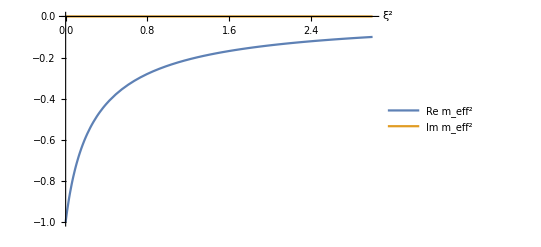

```mathematica
Show[
Plot[{Re[meff2],Im[meff2]}/.posMassRep/.ξ->√ξ2//Evaluate,{ξ2,0.,3},
AxesLabel->{"ξ^2",None},
PlotLegends->Placed[{"Re m_eff^2","Im m_eff^2"},{Right,Bottom}],
PlotRange->Full
]
]
Export[path<>"meff_pos.pdf",%];
```

Plot velocities.
We don’t plot the refractive index since it equals the group velocity.

```mathematica
plotPosRe[ξ2_]:=Module[{ϵv=1,v,vl},
v={vpSol[ω],vgSol[ω]}/.{ϵ->ϵv,ξ->√ξ2};
vl={vpl[ω],vgl[ω], 1}/.{ϵ->ϵv};
Show[
Plot[v,{ω,0.1,10},
AxesLabel->Automatic,
PlotStyle->Opacity[0.5],
PlotLegends->LineLegend[{"v_p(ω)","v_g(ω)"},LegendLabel->"non-local"],
PlotRange->{0.5,1.5}
],
Plot[vl,{ω,0.1,10},
AxesLabel->Automatic,
PlotStyle->Directive[Dashed,Opacity[1]],PlotLegends->LineLegend[{"Re v_p(ω)","Re v_g(ω)","v_wf"},LegendLabel->"local"]
],ImageSize->Medium
]
];
```

```mathematica
Manipulate[
GraphicsColumn[
{plotPosRe[ξ2]},
ImageSize->Large
],
{{ξ2,0.001,"ξ^2"},0.001,1}
]
```

```mathematica
Export[path<>"velocities_pos.pdf",plotPosRe[0.1]];
```

### Negative mass-squared (tachyon)

Local limit

```mathematica
localDev[meff2/.negMassRep]
m02=localDev[meff2/.negMassRep,0]//Normal;
```

1+4 ξ^2+O[ξ]^3

Critical value

```mathematica
meff2/.ξcRep/.negMassRep//Simplify//N
```

3.31107

Complex values

```mathematica
√(ξ^2+1)/.ξcRep/.negMassRep//N
```

1.0564

```mathematica
meff2/.ξ->{√(ξ^2+0.001)/.ξcRep}/.negMassRep//Simplify//N
meff2/.ξ->{√(ξ^2+0.186319417545)/.ξcRep}/.negMassRep//Simplify//N
meff2/.ξ->{√(ξ^2+0.2)/.ξcRep}/.negMassRep//Simplify//N
```

{3.25545-0.490339 ⅈ}

{3.68328×10^-12-1.73205 ⅈ}

{-0.0616054-1.67922 ⅈ}

```mathematica
ξ^2+0.186319417545/.ξcRep/.negMassRep
√%
```

0.3023

0.549818

Highly non-local limit
This behaves effectively as a positive mass-squared scalar with local cubic interaction.

```mathematica
meff2/.negMassRep/.ξ->10//N
```

-1.

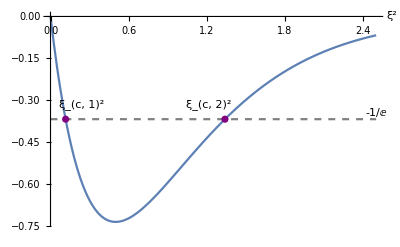

```mathematica
Show[
Plot[Warg/.negMassRep/.ξ->√ξ2//Evaluate,{ξ2,0,2.5},
AxesLabel->{"ξ^2",""},
PlotRange->Full,
MaxRecursion->15
],
Plot[Labeled[-1/ⅇ,"-1/ⅇ",{Right,Center},Spacings->{Automatic,100}],{ξ2,0,2.5},
PlotStyle->{Gray,Dashed}
],
ListPlot[{Labeled[{ξc^2,-1/ⅇ},"ξ_(c, 1)^2"],Labeled[{ξc2^2,-1/ⅇ},"ξ_(c, 2)^2"]},
PlotStyle->Purple
]
]
Export[path<>"meff_neg_Warg.pdf",%];
```

Plot effective mass-squared.

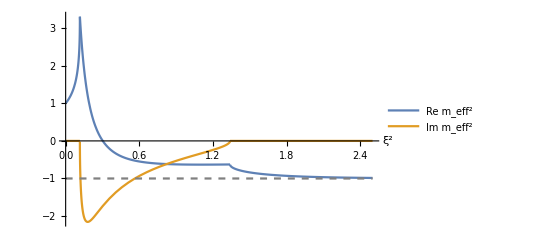

```mathematica
Show[
Plot[{Re[meff2],Im[meff2]}/.negMassRep/.ξ->√ξ2//Evaluate,{ξ2,0,2.5},
AxesLabel->{"ξ^2",None},
PlotLegends->Placed[{"Re m_eff^2","Im m_eff^2"},{Right,Top}],
PlotRange->Full,
MaxRecursion->15
],
Plot[-1,{ξ2,0,2.5},
PlotStyle->{Gray,Dashed}
]
(*Plot[-π/(4ξ2),{ξ2,0,2.5},
PlotStyle->{Brown,Dashed}
]*)
]
Export[path<>"meff_neg.pdf",%];
```

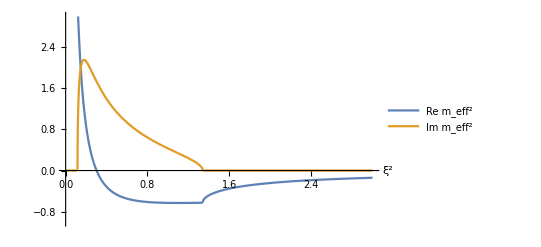

```mathematica
Show[
Plot[{Re[meff2Br],Im[meff2Br]}/.negMassRep/.ξ->√ξ2//Evaluate,{ξ2,0.,3},
AxesLabel->{"ξ^2",None},
PlotLegends->Placed[{"Re m_eff^2","Im m_eff^2"},{Right,Top}],
PlotRange->{-1,3},
MaxRecursion->15
]
]
Export[path<>"meff_neg_W-1.pdf",%];
```

Plot refractive index and velocities.
I am adding a sign by hand for the imaginary part of the local phase velocity: I think there may be a sign problem when taking the square root.

```mathematica
plotNegRe[ξ2_]:=Module[{ϵv=-1,v,vl},
v={Re[vpSol[ω]],Re[vgSol[ω]]}/.{ϵ->ϵv,ξ->√ξ2};
vl={vpl[ω],vgl[ω], 1}/.{ϵ->ϵv};
Show[
Plot[v,{ω,0.1,10},
AxesLabel->Automatic,
PlotStyle->Opacity[0.5],
PlotLegends->LineLegend[{"Re v_p(ω)","Re v_g(ω)"},LegendLabel->"non-local"],
PlotRange->{0,1.5}
],
Plot[vl,{ω,0.1,10},
AxesLabel->Automatic,
PlotStyle->Directive[Dashed,Opacity[1]],PlotLegends->LineLegend[{"Re v_p(ω)","Re v_g(ω)","v_wf"},LegendLabel->"local"]
],ImageSize->Medium
]
];

plotNegIm[ξ2_]:=Module[{ϵv=-1,v,vl},
v={Im[vpSol[ω]],Im[vgSol[ω]]}/.{ϵ->ϵv,ξ->√ξ2};
vl={-Im[vpl[ω]],Im[vgl[ω]]}/.{ϵ->ϵv};
Show[
Plot[v,{ω,0.1,10},
AxesLabel->Automatic,
PlotStyle->Opacity[0.5],
PlotLegends->LineLegend[{"Im v_p(ω)","Im v_g(ω)"},LegendLabel->"non-local"],
PlotRange->{-0.75,1}
],
Plot[vl,{ω,0.1,10},
AxesLabel->Automatic,
PlotStyle->Directive[Dashed,Opacity[1]],PlotLegends->LineLegend[{"Im v_p(ω)","Im v_g(ω)"},LegendLabel->"local"]
],ImageSize->Medium
]
];
```

```mathematica
Manipulate[
GraphicsColumn[
{plotNegRe[ξ2],plotNegIm[ξ2]},
ImageSize->Large
],
{{ξ2,0.001,"ξ^2"},0.001,1.5}
]
```

```mathematica
ξ^2/.ξcRep/.negMassRep//N

Export[path<>"velocities_neg_re_sub_xi1.pdf",plotNegRe[0.05]];
Export[path<>"velocities_neg_im_sub_xi1.pdf",plotNegIm[0.05]];

Export[path<>"velocities_neg_re_complex.pdf",plotNegRe[0.2]];
Export[path<>"velocities_neg_im_complex.pdf",plotNegIm[0.2]];

Export[path<>"velocities_neg_re_sup_xi2.pdf",plotNegRe[1.5]];
Export[path<>"velocities_neg_im_sup_xi2.pdf",plotNegIm[1.5]];
```

0.11598